## Fig 2 raw data

### 2(a) Phase Diagram

```mathematica
(*symmetric&no dissipation; try to reproduce *)
ClearAll["Global`*"]
γ=0;
A0=-0.3; (*A0=ρbar/2*)
q=1;
phase[A_,ω_]:=Module[{T,sol,ImΛ},T=2π/ω;sol=NDSolve[{Rt2'[x]+q/2(A0+A Cos[ω x]) -2 It2[x]q(1+A0+A Cos[ω x])-2(Rt2[x]^2-It2[x]^2)q (A0+A Cos[ω x])==0,It2'[x]+2 Rt2[x]q(1+A0+A Cos[ω x])- 4(Rt2[x]It2[x]) q (A0+A Cos[ω x])==0,Rt2[0]==Rt2[T],It2[0]==It2[T]},{Rt2,It2},{x,0,2T}];ImΛ=2/T NIntegrate[(A0+A Cos[ω x])Evaluate[Rt2[x]]/.sol[[1]][[1]],{x,0,T}];2Abs[ImΛ]];
```

```mathematica
phase[1.1,2]
```

1.03263

```mathematica
Stab=Table[{invω,A,phase[A,1/invω]},{A,0,0.2,0.005},{invω,0.01,2.05,0.02}];
```

```mathematica
Stabplot=Flatten[Chop[Stab],1];
```

```mathematica
(*TODO: Save the calculation*)
Export["/users/linzhixing/desktop/stab.txt",Stabplot,"Table"];
```

```mathematica
Stabtest=Import["/users/linzhixing/desktop/data/stab.txt", "Table"];
```

```mathematica
Stabtest
```

{{0.01,0,0},{0.03,0,0},{0.05,0,0},{0.07,0,0},{0.09,0,0},{0.11,0,0},4189,{3.91,0.2,6.24291×10^-9},{3.93,0.2,8.55093×10^-9},{3.95,0.2,1.1264×10^-8},{3.97,0.2,1.35684×10^-8},{3.99,0.2,1.4269×10^-8}}
 |  |  |  |

```mathematica
(*Analytical method*)
A0=-0.3;
boundary=Table[{invω,A,If[PossibleZeroQ[Im[ArcCos[MathieuC[4(1+2A0)invω^2,-4A invω^2,π]]]/π],0,1]},{A,0,0.2,0.001},{invω,0.01,2.05,0.005}];
boundplot=Flatten[boundary,1];
```

```mathematica
(*save the data*)
Export["/users/linzhixing/desktop/boundary.txt",boundplot,"Table"];
```

### 2(b) ImΛ plot

```mathematica
ClearAll["Global`*"]
```

```mathematica
A0=-0.3;
Lambda[A_,ω_,q_]:=Module[{T,sol,ImΛ},T=(2 π)/ω;sol=NDSolve[{Rt2'[x]+1/2 q (A0+A Cos[ω x])-2 It2[x] q (1+A0+A Cos[ω x])-2 (Rt2[x]^2-It2[x]^2) q (A0+A Cos[ω x])==0,It2'[x]+2 Rt2[x] q (1+A0+A Cos[ω x])-4 (Rt2[x] It2[x]) q (A0+A Cos[ω x])==0,Rt2[0]==Rt2[T],It2[0]==It2[T]},{Rt2,It2},{x,0,2 T}];ImΛ=(2 NIntegrate[(A0+A Cos[ω x]) Evaluate[Rt2[x]]/.sol⟦1⟧⟦1⟧,{x,0,T}])/T;2 Abs[ImΛ]];
```

```mathematica
(*Im Lambda plots*)
st1=Table[{invω,Lambda[0.05,1/invω,1]},{invω,0.01,4,0.01}];
st2=Table[{invω,Lambda[0.1,1/invω,1]},{invω,0.01,4,0.01}];
st3=Table[{invω,Lambda[0.15,1/invω,1]},{invω,0.01,4,0.01}];
st4=Table[{invω,Lambda[0.18,1/invω,1]},{invω,0.01,4,0.01}];
```

```mathematica
(*TODO: save the calculations*)
Export["/users/linzhixing/desktop/data/Lambda_symm_5.txt",st1,"Table"];
Export["/users/linzhixing/desktop/data/Lambda_symm_10.txt",st2,"Table"];
Export["/users/linzhixing/desktop/data/Lambda_symm_15.txt",st3,"Table"];
Export["/users/linzhixing/desktop/data/Lambda_symm_18.txt",st4,"Table"];
```

## Fig 3 raw data

### 3(b) Decay rate

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Set the parameters*)
A0=-0.3;
β=1;
```

```mathematica
(*Pack the correlator calculation codes into a function*)
(*The function Correlator gives the time evolution of correlators, the period and the stability information*)
Correlator[γ_,A_,ω_,q_]:=Module[{T,t0,t0sol,t1,t1sol,t2,t2sol,Λ,n,m,nt,mt,mt1,G2sol,g2,g3sol,g3,g4sol,g4,λ,λ1,ωt,γnF,γmF,γmF1,colsol},T=2π/ω;
(*Solve t2*)
t2sol=NDSolve[{Rt2'[x]+q/2(A0+A Cos[ω x]) -2 It2[x]q(1+A0+A Cos[ω x])-2(Rt2[x]^2-It2[x]^2)q (A0+A Cos[ω x])==0,It2'[x]+2 Rt2[x]q(1+A0+A Cos[ω x])- 4(Rt2[x]It2[x]) q (A0+A Cos[ω x])==0,Rt2[0]==Rt2[T],It2[0]==It2[T]},{Rt2,It2},{x,0,4T}];
t2[t_]:=(Rt2[t]/.t2sol[[1,1]])+I(It2[t]/.t2sol[[1,2]]);
(*Solve t1*)
t1sol=NDSolve[{y'[x]+(1+8y[x]t2[x])q/2(A0+A Cos[ω x])-2I q(1+A0+A Cos[ω x])y[x]==0,y[0]==y[T]},{y},{x,0,4T}];
t1[t_]:=y[t]/.t1sol[[1]];
(*Solve Λ*)
Λ=1/T NIntegrate[(1+A0+A Cos[ω x])+2I (A0+A Cos[ω x])t2[x],{x,0,T}];
(*Solve t0*)
t0sol=NDSolve[{y'[x]+q(1+A0+A Cos[ω x])+2I q(A0+A Cos[ω x])t2[x]==0,y[0]==0},y,{x,0,4T}];
t0[t_]:=(y[t]/.t0sol[[1]])+q Λ t;
(*Define n&m*)
n[t_]:=-1/2+(1+A0+A Cos[ω t])/(2 √(1+2(A0+A Cos[ω t])))Coth[(β q)/2 √(1+2(A0+A Cos[ω t]))];
m[t_]:=-(A0+A Cos[ω t])/(2 √(1+2(A0+A Cos[ω t])))Coth[(β q)/2 √(1+2(A0+A Cos[ω t]))];
(*Define nt, mt & mt1*)
nt[t_?NumericQ]:=Evaluate@-1/2+(n[t]+1/2)(1+8t1[t]t2[t])+2I t1[t]m[t]-2I t2[t](1+4t1[t]t2[t])m[t];
mt[t_?NumericQ]:=Evaluate@Exp[-2I t0[t]](m[t]-4I t2[t](n[t]+1/2)-4t2[t]^2 m[t]);
mt1[t_?NumericQ]:=Evaluate@Exp[2I t0[t]](m[t](1+4t1[t]t2[t])^2+4I t1[t](1+4t1[t]t2[t])(n[t]+1/2)-4t1[t]^2m[t]);
(*Solve g2*)
G2sol=NDSolve[{y'[x]+γ q(1+Cos[ω x])y[x]-γ q(1+Cos[ω x])(nt[x]+1/2)==0,y[0]==y[T]},{y},{x,0,4T}];
g2[t_]:=-Log[(y[t]/.G2sol[[1,1]])+1/2]; 
(*Solve g3*)
g3sol=NDSolve[{y'[x]+(γ q(1+Cos[ω x])+2I Λ q)y[x]-γ q(1+Cos[ω x])mt[x]==0,y[0]==y[T]},{y},{x,0,4T}];
g3[t_]:=y[t]/.g3sol[[1]];
(*Solve g4*)
g4sol=NDSolve[{y'[x]+(γ q(1+Cos[ω x])-2I Λ q)y[x]-γ q(1+Cos[ω x])mt1[x]==0,y[0]==y[T]},{y},{x,0,4T}];
g4[t_]:=y[t]/.g4sol[[1]];
λ=4 I t1[0] Λ;
λ1=-4I t2[0](1+4t1[0] t2[0])Λ;
ωt=Λ(1+8 t1[0] t2[0]);
(*here we use t0[0]=0*)
γnF=-γ/2+γ(1+8t1[0]t2[0])(Exp[-g2[0]]-1/2)-2I g3[0] t1[0] (1+4t1[0] t2[0])(γ+2I Λ)+ 2I g4[0] t2[0](γ-2I Λ);
γmF=4γ I t2[0](Exp[-g2[0]]-1/2)(1+4t1[0] t2[0])-4g4[0] t2[0]^2(γ-2I Λ)+g3[0] (1+4t1[0] t2[0])^2(γ+2I Λ);
γmF1=-4I γ t1[0](Exp[-g2[0]]-1/2)+g4[0](γ-2I Λ)-4g3[0] t1[0]^2 (γ+2I Λ);
colsol=NDSolve[{n1'[t]==q(I λ m1[t]-I λ1 m2[t]+γnF-γ n1[t]),n2'[t]==q(I λ m1[t]-I λ1 m2[t]+γnF-γ n2[t]),m1'[t]==q((-2I ωt-γ) m1[t]-I λ1(1+n1[t]+n2[t])+γmF),m2'[t]==q((2I ωt-γ) m2[t]+I λ(1+n1[t]+n2[t])+γmF1),n1[0]==0,n2[0]==0,m1[0]==0,m2[0]==0},{n1,n2,m1,m2},{t,0,200T}];
{colsol,T,γ-2Abs[Im[Λ]]}];
```

```mathematica
(*Stable fitting*)
DecayFitStable[corr_,a0_,b0_,num_]:=Module[{data,nlm,corrsol,tw,stab},{corrsol,tw,stab}=corr;data=Table[{s,Evaluate@Re[n1[s]/.corrsol[[1,1]]]},{s,0,num tw,tw}];
nlm = NonlinearModelFit[data, a (1-Exp[b x]),{{a,a0},{b,b0}},x];
{Show[ListPlot[data],Plot[nlm[t],{t,0,num tw}, PlotRange->All,PlotStyle->Orange],Frame->True,PlotLabel->Normal[nlm]],a/.nlm["BestFitParameters"],b/.nlm["BestFitParameters"]}]
```

```mathematica
(*test*)
```

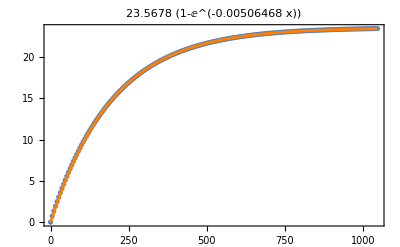
{-Graphics-,23.5678,-0.00506468}

```mathematica
DecayFitStable[Correlator[0.15,0.1,1.2,1],0.5,-0.5,200]
```

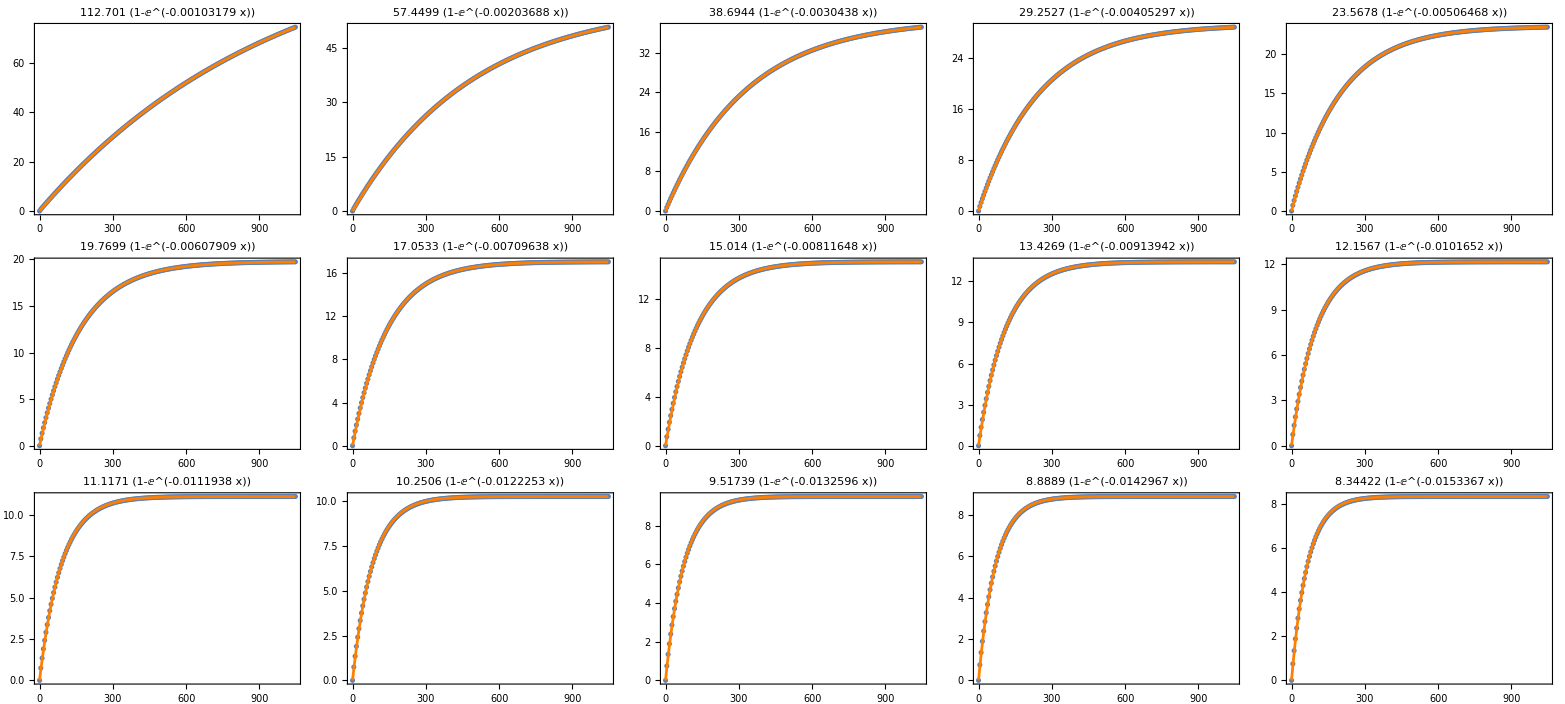

```mathematica
Grid[ArrayReshape[Table[DecayFitStable[Correlator[γt,0.1,1.2,1],0.5,-0.5,200][[1]],{γt,0.146,0.16,0.001}],{3,5}]]
```

```mathematica
(*Unstable fitting*)
DecayFitStable[corr_,a0_,b0_,num_]:=Module[{data,nlm,corrsol,tw,stab},{corrsol,tw,stab}=corr;data=Table[{s,Evaluate@Re[n1[s]/.corrsol[[1,1]]]},{s,0,num tw,tw}];
nlm = NonlinearModelFit[data, a (1-Exp[b x]),{{a,a0},{b,b0}},x];
{Show[ListPlot[data],Plot[nlm[t],{t,0,num tw}, PlotRange->All,PlotStyle->Orange],Frame->True,PlotLabel->Normal[nlm]],a/.nlm["BestFitParameters"],b/.nlm["BestFitParameters"]}]
```

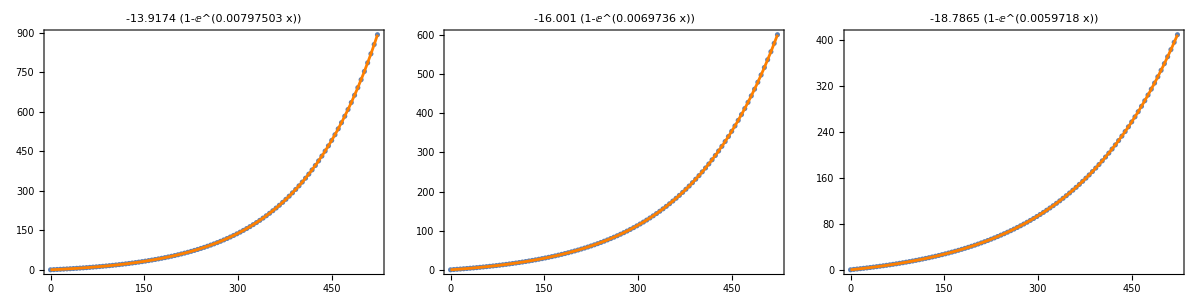

```mathematica
Grid[ArrayReshape[Table[DecayFitStable[Correlator[γt,0.1,1.2,1],0.5,0.008,100][[1]],{γt,0.137,0.139,0.001}],{1,3}]]
```

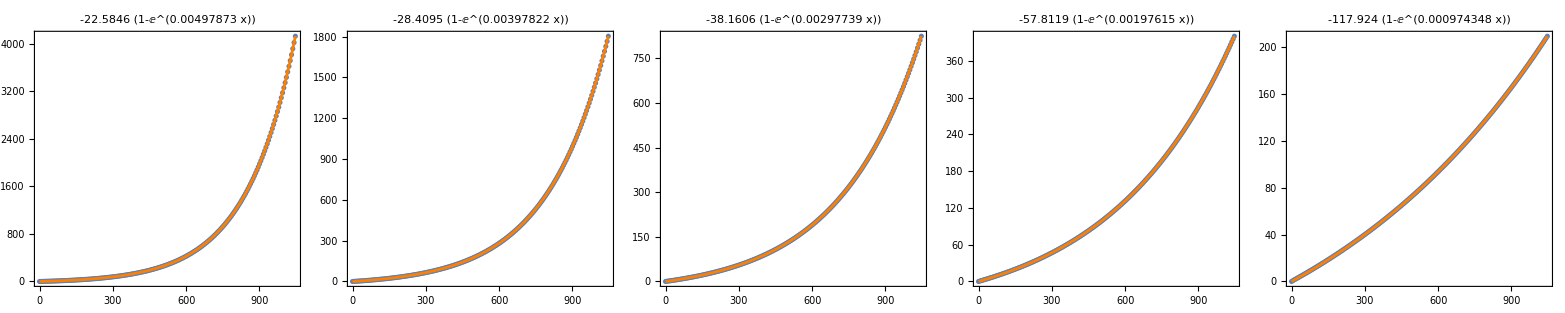

```mathematica
Grid[ArrayReshape[Table[DecayFitStable[Correlator[γt,0.1,1.2,1],0.5,0.008,200][[1]],{γt,0.140,0.144,0.001}],{1,5}]]
```

## Fig 4 raw data

### 4(a) phase diagram & 4(c)-(d)

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*calculate ImΛn+ImΛp*)
A0=-0.3;
(*for chiral instability, chiralPR=0*)
chiralPR[γ_,A_,ω_,q_]:=Module[{T,sol1,sol2,ImΛp,ImΛn},T=2π/ω;sol1=NDSolve[{Rt2'[x]+q/2(A0+A Cos[ω x]) -2 It2[x]q(1+A0+A Cos[ω x])-Rt2[x]q γ(1+Cos[ω x])/2-2(Rt2[x]^2-It2[x]^2)q (A0+A Cos[ω x])==0,It2'[x]+2 Rt2[x]q(1+A0+A Cos[ω x])-It2[x]q γ(1+Cos[ω x])/2- 4(Rt2[x]It2[x]) q (A0+A Cos[ω x])==0,Rt2[0]==Rt2[T],It2[0]==It2[T]},{Rt2,It2},{x,0,2T}];
sol2=NDSolve[{Rs2'[x]+q/2(A0+A Cos[ω x])-2 Is2[x]q(1+A0+A Cos[ω x])+Rs2[x]q γ(1+Cos[ω x])/2-2(Rs2[x]^2-Is2[x]^2)q (A0+A Cos[ω x])==0,Is2'[x]+2 Rs2[x]q(1+A0+A Cos[ω x])+Is2[x]q γ(1+Cos[ω x])/2- 4(Rs2[x]Is2[x]) q (A0+A Cos[ω x])==0,Rs2[0]==Rs2[T],Is2[0]==Is2[T]},{Rs2[x],Is2[x]},{x,0,2T}];ImΛn=γ/4+2/T NIntegrate[(A0+A Cos[ω x])Evaluate[Rt2[x]]/.sol1[[1]][[1]],{x,0,T}];
ImΛp=-γ/4+2/T NIntegrate[(A0+A Cos[ω x])Evaluate[Rs2[x]]/.sol2[[1]][[1]],{x,0,T}];ImΛn+ImΛp]
```

```mathematica
(*test case*)
chiralPR[0.23,0.2,1.25,1]
```

5.79169×10^-9

```mathematica
(*phase diagram*)
PRdiagram=Table[{invω,A,chiralPR[0.05,A,1/invω,1]},{A,0,0.2,0.005},{invω,0.01,2,0.01}];
```

```mathematica
PRplot=Flatten[Chop[PRdiagram],1]
```

{{0.01,0,1.61803×10^-9},{0.02,0,-1.96163×10^-10},{0.03,0,9.22727×10^-10},{0.04,0,1.69424×10^-9},{0.05,0,1.93672×10^-10},{0.06,0,0},8189,{1.96,0.2,3.51429×10^-8},{1.97,0.2,5.71152×10^-8},{1.98,0.2,5.0679×10^-8},{1.99,0.2,4.11205×10^-8},{2.,0.2,4.20552×10^-8}}
 |  |  |  |

```mathematica
(*TODO: Save the calculation*)
Export["/users/linzhixing/desktop/chiralPR.txt",PRplot,"Table"];
```

```mathematica
(*ImΛn+ImΛp dependence with γ under 1/ω with A=0.1*)
pr1=Table[{γ,chiralPR[γ,0.1,1.0,1]},{γ,0.00,0.1,0.001}]; (*stable*)
pr2=Table[{γ,chiralPR[γ,0.1,1.2,1]},{γ,0.00,0.1,0.001}]; 
pr3=Table[{γ,chiralPR[γ,0.1,1.4,1]},{γ,0.00,0.1,0.001}];
```

```mathematica
(*save the data*)
Export["/users/linzhixing/desktop/chiral_1_10.txt",pr1,"Table"]
Export["/users/linzhixing/desktop/chiral_1_12.txt",pr2,"Table"]
Export["/users/linzhixing/desktop/chiral_1_14.txt",pr3,"Table"]
```

/users/linzhixing/desktop/chiral_1_10.txt

/users/linzhixing/desktop/chiral_1_12.txt

/users/linzhixing/desktop/chiral_1_14.txt

```mathematica
(*ImΛn+ImΛp dependence with γ under different A with ω=1.25*)
(*all unstable*)
prA1=Table[{γ,chiralPR[γ,0.1,1.25,1]},{γ,0.00,0.3,0.01}]; 
prA2=Table[{γ,chiralPR[γ,0.15,1.25,1]},{γ,0.00,0.3,0.01}]; 
prA3=Table[{γ,chiralPR[γ,0.18,1.25,1]},{γ,0.00,0.3,0.01}];
```

```mathematica
(*save the data*)
Export["/users/linzhixing/desktop/data/chiral_10_125.txt",prA1,"Table"];
Export["/users/linzhixing/desktop/data/chiral_15_125.txt",prA2,"Table"];
Export["/users/linzhixing/desktop/data/chiral_18_125.txt",prA3,"Table"];
```

### 4(b) ImΛ curve

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*chiral coupling phase diagram*)
A0=-0.3; (*A0=ρbar/2*)
Lambda[γ_,A_,ω_,q_]:=Module[{T,sol1,sol2,ImΛp,ImΛn},T=2π/ω;sol1=NDSolve[{Rt2'[x]+q/2(A0+A Cos[ω x]) -2 It2[x]q(1+A0+A Cos[ω x])-Rt2[x]q γ(1+Cos[ω x])/2-2(Rt2[x]^2-It2[x]^2)q (A0+A Cos[ω x])==0,It2'[x]+2 Rt2[x]q(1+A0+A Cos[ω x])-It2[x]q γ(1+Cos[ω x])/2- 4(Rt2[x]It2[x]) q (A0+A Cos[ω x])==0,Rt2[0]==Rt2[T],It2[0]==It2[T]},{Rt2,It2},{x,0,2T}];
sol2=NDSolve[{Rs2'[x]+q/2(A0+A Cos[ω x])-2 Is2[x]q(1+A0+A Cos[ω x])+Rs2[x]q γ(1+Cos[ω x])/2-2(Rs2[x]^2-Is2[x]^2)q (A0+A Cos[ω x])==0,Is2'[x]+2 Rs2[x]q(1+A0+A Cos[ω x])+Is2[x]q γ(1+Cos[ω x])/2- 4(Rs2[x]Is2[x]) q (A0+A Cos[ω x])==0,Rs2[0]==Rs2[T],Is2[0]==Is2[T]},{Rs2,Is2},{x,0,2T}];ImΛn=γ/4+2/T NIntegrate[(A0+A Cos[ω x])Evaluate[Rt2[x]]/.sol1[[1]][[1]],{x,0,T}];
ImΛp=-γ/4+2/T NIntegrate[(A0+A Cos[ω x])Evaluate[Rs2[x]]/.sol2[[1]][[1]],{x,0,T}];{4Abs[ImΛn]-γ,4Abs[ImΛp]-γ}];
```

```mathematica
(*test*)
Lambda[0.25,0.1,1/0.8,1]
```

{0.168605,0.168605}

```mathematica
st1=Table[{invω,Lambda[0.1,0.05,1/invω,1][[1]]},{invω,0.01,4,0.01}];
st2=Table[{invω,Lambda[0.1,0.1,1/invω,1][[1]]},{invω,0.01,4,0.01}];
st3=Table[{invω,Lambda[0.1,0.15,1/invω,1][[1]]},{invω,0.01,4,0.01}];
st4=Table[{invω,Lambda[0.1,0.18,1/invω,1][[1]]},{invω,0.01,4,0.01}];
```

```mathematica
Export["/users/linzhixing/desktop/data/Lambda_01_5.txt",st1,"Table"];
Export["/users/linzhixing/desktop/data/Lambda_01_10.txt",st2,"Table"];
Export["/users/linzhixing/desktop/data/Lambda_01_15.txt",st3,"Table"];
Export["/users/linzhixing/desktop/data/Lambda_01_18.txt",st4,"Table"];
```